-Graphics-

```mathematica
n=8;m=4;
```

```mathematica
inrange[{x_,y_}]:=(1≤x≤n)&&(1≤y≤m)
```

```mathematica
dirs={{1,1},{1,0},{1,-1},{0,-1},{-1,-1},{-1,0},{-1,1},{0,1},{1,1},{1,0}};
```

```mathematica
next[L_]:=Module[{temp},
temp=Select[Flatten[Position[dirs,L]],1<#<10&][[1]];
dirs[[temp-1;;temp+1]]]
```

```mathematica
nearby[loc_]:=Map[loc+#&,Union[dirs]]
```

```mathematica
n=8;m=4;initialize:=Module[{i,j},stack=Flatten[Table[{{i,j},{i+1,j}},{i,2,n-2},{j,1,m}],1];
solns={};
While[Length[stack]>0,
cur=First[stack];
stack=Rest[stack];
pos=Last[cur];
If[pos==First[cur],If[MemberQ[next[cur[[1]]-cur[[2]]],cur[[-2]]-cur[[1]]],AppendTo[solns,cur]],
dir=cur[[-1]]-cur[[-2]];
poss=Map[pos+#&,next[dir]];
new=Select[poss,inrange[#]&& Not[MemberQ[Rest[cur],#]]&&(Sort[{Reverse[First[cur]],Reverse[#]}]=={Reverse[First[cur]],Reverse[#]})&];
stack=Map[Join[cur,{#}]&,new]~Join~stack;
]]]
```

```mathematica
pic[s_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,m}],
Table[Line[{{i,0},{i,m}}],{i,0,n}],
Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,s]]
},ImageSize->{20n+1,20m+1}],Antialiasing->False]
```

```mathematica
afterpic[s_,r_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,m}],
Table[Line[{{i,0},{i,m}}],{i,0,n}],
Map[Text[Style[#[[1]],FontSize->16],#[[2]]-{1/2,1/2}]&,r],
Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,s]]
},ImageSize->{20n+1,20m+1},PlotRange->{{-.01,n+.01},{-.01,m+.01}}],Antialiasing->False]
```

```mathematica
anotherpic[s_,r1_,r2_]:=Style[Graphics[{
Hue[1/3,1/3],Map[Rectangle[#-{1,1},#]&,r1],
Hue[0,1/3],Map[Rectangle[#-{1,1},#]&,r2],
Black,Table[Line[{{0,i},{n,i}}],{i,0,m}],
Table[Line[{{i,0},{i,m}}],{i,0,n}],
Blue,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,s]]
},ImageSize->{20n+1,20m+1},PlotRange->{{-.01,n+.01},{-.01,m+.01}}],Antialiasing->False]
```

```mathematica
rn:=Module[{q},q={RandomInteger[{1,n}],RandomInteger[{1,m}]};
While[q=={1,1}||q=={n,m}||q=={1,m}||q=={n,1},q={RandomInteger[{1,n}],RandomInteger[{1,m}]}];q]
```

```mathematica
uniqueQ[p_,q_]:=Module[{},
s=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Length[s]==1]
```

```mathematica
choose[L_,p_,n_]:=Select[L,Not[MemberQ[#,p]]&&(Length[Intersection[Rest[#],nearby[p]]]==n)&]
```

```mathematica
n=5;m=5;Print[Timing[initialize]];Length[solns]
```

{0.017657,Null}

15

```mathematica
n=6;m=5;Print[Timing[initialize]];Length[solns]
```

{0.067787,Null}

48

```mathematica
n=7;m=5;Print[Timing[initialize]];Length[solns]
```

{0.274071,Null}

120

```mathematica
n=8;m=5;Print[Timing[initialize]];Length[solns]
```

{1.31092,Null}

348

```mathematica
n=6;m=6;Print[Timing[initialize]];Length[solns]
```

{0.447225,Null}

239

```mathematica
n=7;m=6;Print[Timing[initialize]];Length[solns]
```

{3.46881,Null}

1195

```mathematica
n=8;m=6;Print[Timing[initialize]];Length[solns]
```

{29.6048,Null}

7223

```mathematica
n=7;m=7;Print[Timing[initialize]];Length[solns]
```

{49.456,Null}

13961

```mathematica
n=8;m=7;Print[Timing[initialize]];Length[solns]
```

{2035.55,Null}

162953

```mathematica
n=9;m=6;Print[Timing[initialize]];Length[solns]
```

{363.804,Null}

50113

```mathematica
n=10;m=6;Print[Timing[initialize]];Length[solns]
```

{11127.4,Null}

407515

## 5x5 inside

```mathematica
For[i=1,i≤n/2,i++,
For[j=1,j≤i,j++,
For[k=0,k≤8,k++,
s=choose[solns,{i,j},k];
If[Length[s]==1,Print[afterpic[s[[1]],{{k,{i,j}}}]]]]]]
```

-Graphics-

-Graphics-

-Graphics-

## 6x6 inside

```mathematica
For[i=1,i≤n/2,i++,
For[j=1,j≤n/2,j++,
For[k=0,k≤8,k++,
For[ii=i,ii≤n+1-i,ii++,
For[jj=1,jj≤n+1-j,jj++,
For[kk=0,kk≤8,kk++,
s=choose[choose[solns,{i,j},k],{ii,jj},kk];
If[Length[s]==1,Print[afterpic[s[[1]],{{k,{i,j}},{kk,{ii,jj}}}]]]]]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«286 more identical outputs»

## 7x7 inside

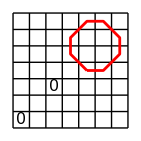

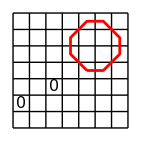

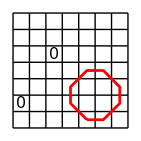

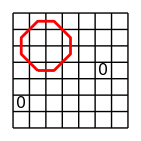

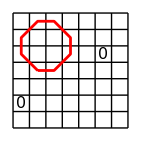

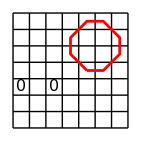

-Graphics-

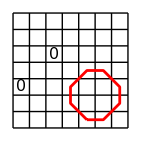

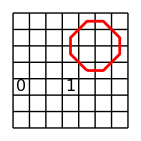

-Graphics-

-Graphics-

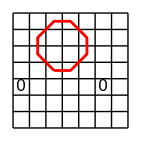

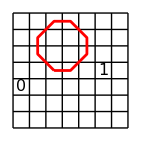

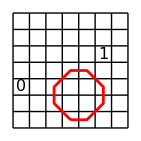

-Graphics-

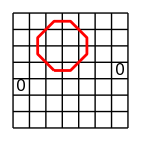

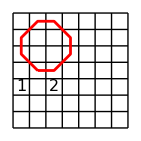

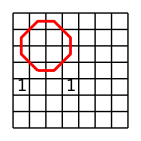

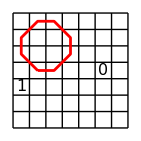

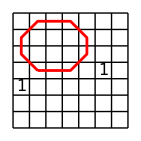

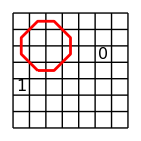

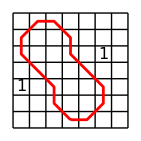

-Graphics-

-Graphics-

-Graphics-

-Graphics-

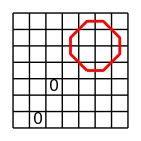

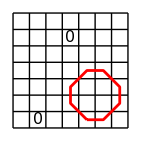

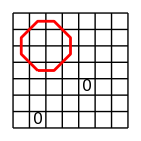

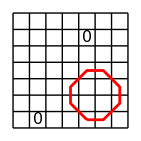

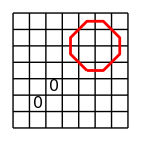

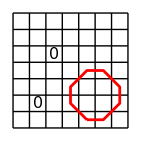

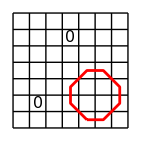

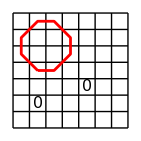

-Graphics-

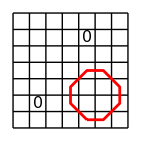

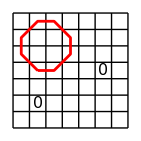

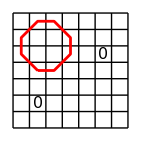

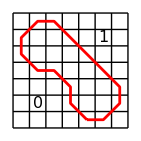

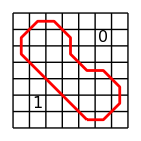

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

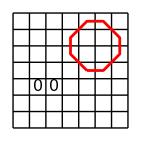

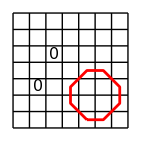

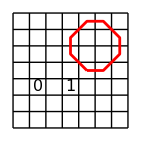

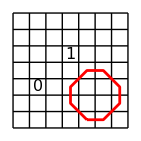

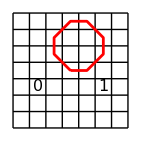

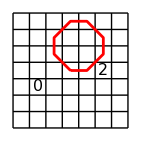

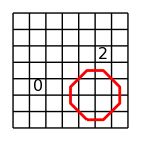

-Graphics-

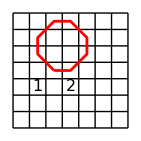

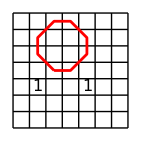

-Graphics-

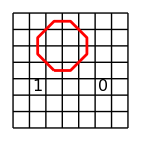

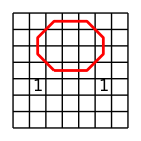

-Graphics-

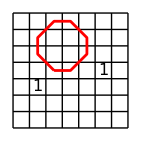

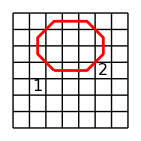

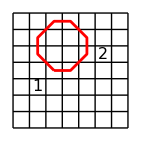

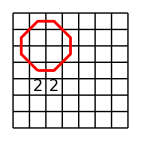

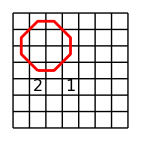

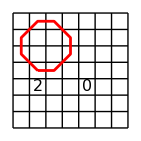

-Graphics-

-Graphics-

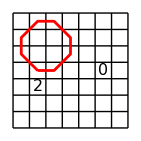

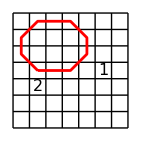

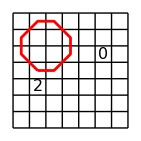

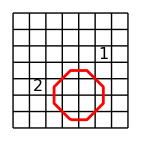

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

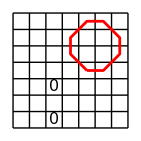

-Graphics-

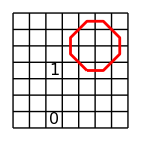

-Graphics-

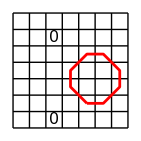

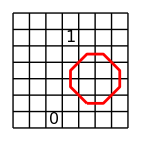

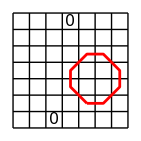

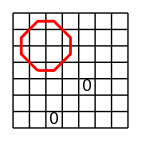

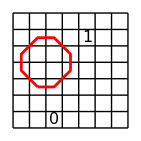

-Graphics-

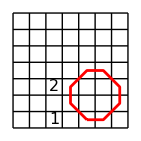

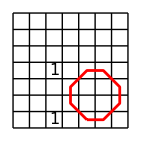

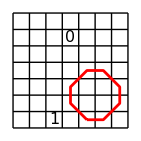

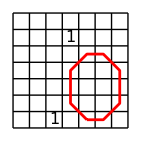

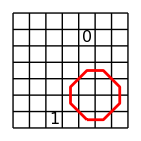

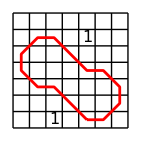

-Graphics-

-Graphics-

-Graphics-

-Graphics-

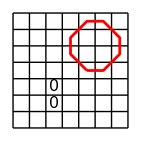

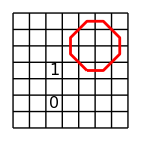

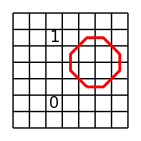

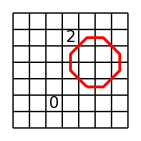

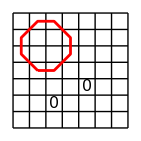

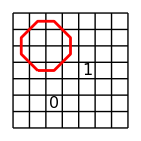

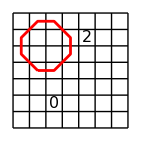

-Graphics-

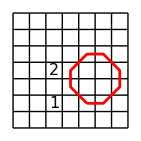

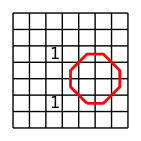

-Graphics-

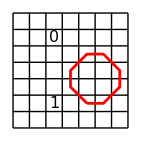

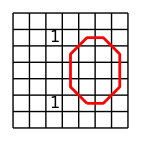

-Graphics-

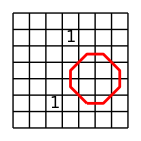

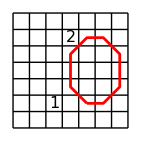

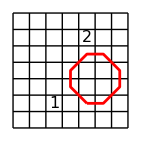

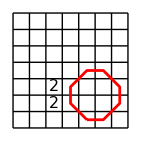

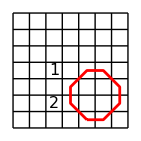

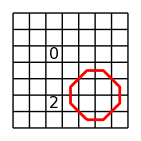

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«32 more identical outputs»

```mathematica
For[i=1,i≤n/2,i++,
For[j=1,j≤n/2,j++,
For[k=0,k≤8,k++,
For[ii=i,ii≤n+1-i,ii++,
For[jj=1,jj≤n+1-j,jj++,
For[kk=0,kk≤8,kk++,
s=choose[choose[solns,{i,j},k],{ii,jj},kk];
If[Length[s]==1,Print[afterpic[s[[1]],{{k,{i,j}},{kk,{ii,jj}}}]]]]]]]]]
```

## 6x6 colors

```mathematica
yes=3;no=3;
For[y=1,y>0,y++,
p=Union[Table[rn,{yes}]];
While[Length[p]<yes,p=Union[Table[rn,{yes}]]];
q=Union[Table[rn,{no}]];
While[Length[q]<no||Intersection[p,q]=!={},q=Union[Table[rn,{no}]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
If[Length[p]+Length[q]≤4,sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«105 more identical outputs»

$Aborted

-Graphics-

-Graphics-

-Graphics-

«80 more identical outputs»

$Aborted

## 7x6 colors

```mathematica
yes=4;no=3;
For[y=1,y>0,y++,
p=Union[Table[rn,{yes}]];
While[Length[p]<yes,p=Union[Table[rn,{yes}]]];
q=Union[Table[rn,{no}]];
While[Length[q]<no||Intersection[p,q]=!={},q=Union[Table[rn,{no}]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
If[Length[p]+Length[q]≤4,sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«351 more identical outputs»

$Aborted

## 7x7 colors

```mathematica
yes=4;no=4;
For[y=1,y>0,y++,
p=Union[Table[rn,{yes}]];
While[Length[p]<yes,p=Union[Table[rn,{yes}]]];
q=Union[Table[rn,{no}]];
While[Length[q]<no||Intersection[p,q]=!={},q=Union[Table[rn,{no}]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
If[Length[p]+Length[q]≤6,sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«39 more identical outputs»

## 8x7 colors

```mathematica
For[y=1,y>0,y++,
p=Union[Table[rn,{4}]];
q=Complement[Table[rn,{4}],p];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]];
While[sss>1,
If[Random[]<.5,AppendTo[p,rn];p=Union[p],AppendTo[q,rn];q=Union[q]];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]
```

-Graphics-

-Graphics-

-Graphics-

«39 more identical outputs»

## 9x6 colors

```mathematica
For[y=1,y>0,y++,
p=Union[Table[rn,{4}]];
q=Complement[Table[rn,{4}],p];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]];
While[sss>1,
If[Random[]<.5,AppendTo[p,rn];p=Union[p],AppendTo[q,rn];q=Union[q]];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]
```

-Graphics-

-Graphics-

-Graphics-

«51 more identical outputs»

$Aborted

## 10x6 colors

```mathematica
For[y=1,y>0,y++,
p=Union[Table[rn,{4}]];
q=Complement[Table[rn,{4}],p];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]];
While[sss>1,
If[Random[]<.5,AppendTo[p,rn];p=Union[p],AppendTo[q,rn];q=Union[q]];
sss=Length[Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&]]];
If[uniqueQ[p,q],
For[h=1,h≤Length[p],h++,
If[uniqueQ[Drop[p,{h}],q],p=Drop[p,{h}];h--]];
For[h=1,h≤Length[q],h++,
If[uniqueQ[p,Drop[q,{h}]],q=Drop[q,{h}];h--]];
sss=Select[solns,Length[Intersection[Rest[#],p]]==Length[p]&& Length[Intersection[Rest[#],q]]==0&];
Print[anotherpic[{},p,q]];Print[anotherpic[sss[[1]],p,q]]]]
```

-Graphics-

-Graphics-

-Graphics-

«35 more identical outputs»

$Aborted